# Numerical Solution

- Potential

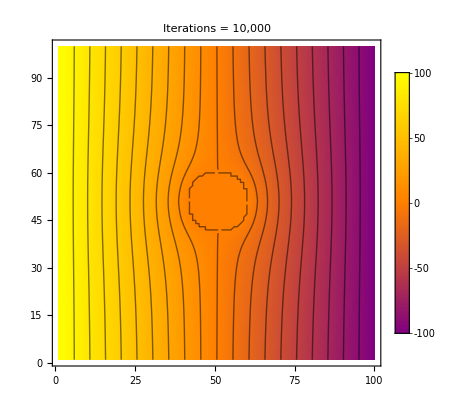

```mathematica
nplatesdata= Import["/home/2317101h/year_3/group_project/numerical_sol/section2.1/plates/laplace.dat"];

nplatesreshape = ArrayReshape[nplatesdata, {100,100}];
epilog=ListContourPlot[nplatesreshape,ContourShading->None, Contours->Function[{min,max},Range[min,max,10]]][[1]];
ListDensityPlot[nplatesreshape,PlotTheme->"Detailed",ColorFunction->(Blend[{Purple,Orange,Yellow},#1]&), Epilog->epilog,PlotLabel->"Iterations = 10,000"]
```

Distance between plates = 100
Voltage of each plate (oppositely charged) = 100
Radius of cylinder = 10
Method = FDM

```mathematica
Export["/home/2317101h/year_3/group_project/analytical_sol/section2.1/plates/analytical_plates.png",ListDensityPlot[ArrayReshape[Import["/home/2317101h/year_3/group_project/analytical_sol/section2.1/plates/plates_anal.dat"],{100,100}],PlotTheme->"Detailed",ColorFunction->(Blend[{Purple,Orange,Yellow},#1]&), Epilog->ListContourPlot[ArrayReshape[Import["/home/2317101h/year_3/group_project/analytical_sol/section2.1/plates/plates_anal.dat"], {100,100}],ContourShading->None, Contours->Function[{min,max},Range[min,max,10]]][[1]]]]
```

/home/2317101h/year_3/group_project/analytical_sol/section2.1/plates/analytical_plates.png

- Create a GIF (Potential)

```mathematica
Do[Export["/home/2317101h/year_3/group_project/numerical_sol/section2.1/plates/anim/pics/"<>ToString[i]<>".png",ListDensityPlot[ArrayReshape[Import["/home/2317101h/year_3/group_project/numerical_sol/section2.1/plates/anim/" <> ToString[i] <> ".dat"],{100,100}],PlotTheme->"Detailed",ColorFunction->(Blend[{Purple,Orange,Yellow},#1]&), Epilog->ListContourPlot[ArrayReshape[Import["/home/2317101h/year_3/group_project/numerical_sol/section2.1/plates/anim/" <> ToString[i] <> ".dat"], {100,100}],ContourShading->None, Contours->Function[{min,max},Range[min,max,10]]][[1]],PlotLabel->"Iterations =" <>ToString[i] ]],{i, 0, 5000, 10}]
```

Analytical Solution

- Potential (using C++)

```mathematica
aplatesdata= Import["/home/2317101h/year_3/group_project/analytical_sol/section2.1/plates/plates_anal.dat"]

aplatesreshape= ArrayReshape[aplatesdata, {100,100}];
```

{{98},{96.0004},{94.0017},{92.0038},{90.0069},{88.011},{86.0162},{84.0225},{82.03},{80.0387},{78.0488},{76.0602},{74.073},{72.0874},{70.1033},{68.1208},{66.14},{64.161},10064,{-64.1089},{-66.0883},{-68.0695},{-70.0525},{-72.0371},{-74.0234},{-76.0112},{-78.0005},{-79.9912},{-81.9832},{-83.9765},{-85.9709},{-87.9666},{-89.9632},{-91.961},{-93.9596},{-95.9592},{}}
 |  |  |  |

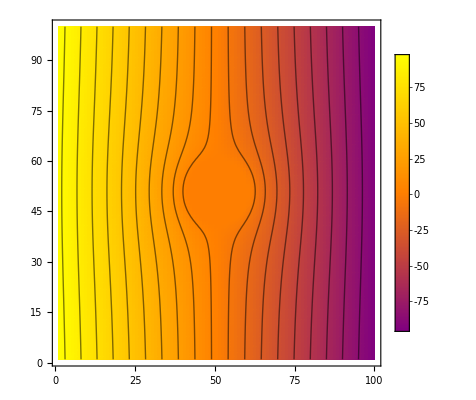

```mathematica
epilog=ListContourPlot[aplatesreshape,ContourShading->None, Contours->Function[{min,max},Range[min,max,10]]][[1]];
ListDensityPlot[aplatesreshape,PlotTheme->"Detailed",ColorFunction->(Blend[{Purple,Orange,Yellow},#1]&), Epilog->epilog]
```

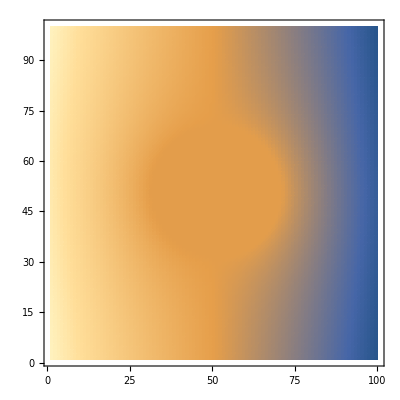

```mathematica
ListDensityPlot[aplatesreshape]
```

- Electric Field (using C++)

```mathematica
efplates= Import["/home/2317101h/year_3/group_project/analytical_sol/section2.1/plates/plates_ef.dat"]

efarrayplates = ArrayReshape[efplates, {100,100}]
```

{{0.0565685},{0.0291398},{0.00115326},{-0.0273997},{-0.0565277},{-0.0862385},{-0.11654},{-0.147439},{-0.178942},{-0.211055},{-0.243783},{-0.277131},{-0.311101},10074,{0.281812},{0.247701},{0.214235},{0.18141},{0.149221},{0.117661},{0.0867245},{0.0564027},{0.0266881},{-0.00242808},{-0.0309547},{-0.058901},{}}
 |  |  |  |

{{0.0565685,0.0291398,0.00115326,-0.0273997,-0.0565277,-0.0862385,-0.11654,-0.147439,-0.178942,-0.211055,-0.243783,-0.277131,-0.311101,-0.345696,72,0.380917,0.345696,0.311101,0.277131,0.243783,0.211055,0.178942,0.147439,0.11654,0.0862385,0.0565277,0.0273997,-0.00115326,-0.0291398},99}
 |  |  |  |

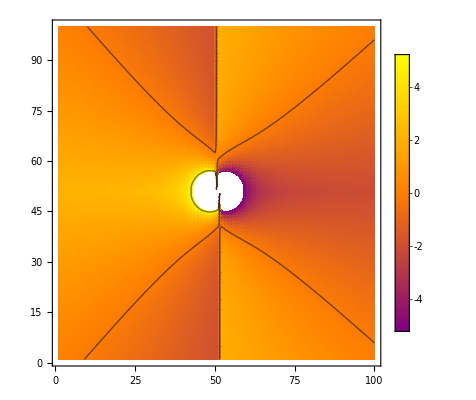

```mathematica
epilog=ListContourPlot[efarrayplates,ContourShading->None, Contours->Function[{min,max},Range[min,max,5]]][[1]];
ListDensityPlot[efarrayplates,PlotTheme->"Detailed",ColorFunction->(Blend[{Purple,Orange,Yellow},#1]&), Epilog->epilog]
```

```mathematica
ListVectorPlot[efplates, VectorPoints->All]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[efplates].

Visualization`Core`ListVectorPlot::vfldata: efplates is not a valid vector field dataset or a valid list of datasets.

ListVectorPlot[efplates,VectorPoints→All]

```mathematica
efsol[x_, y_] = (-50/(Log[5] *Sqrt[x^2+y^2]))
```

-50/(√(x^2+y^2) Log[5])

```mathematica
Plot3D[-50/(√(x^2+y^2) Log[5]),{x,-0.3496526853793498,0.3496526853793498},{y,-0.3496526853793498,0.3496526853793498}]
```

-Graphics3D-

Compare numerical solution to analytical solution

- Potential

```mathematica
comparep2 = nplatesreshape - aplatesreshape
```

{{2,1.955,1.9091,1.8626,1.8154,1.7675,1.719,1.6699,1.6202,1.5701,80,-3.4481,-3.5118,-3.5749,-3.6375,-3.6996,-3.761,-3.8217,-3.8818,-3.941,-3.9996},99}
 |  |  |  |

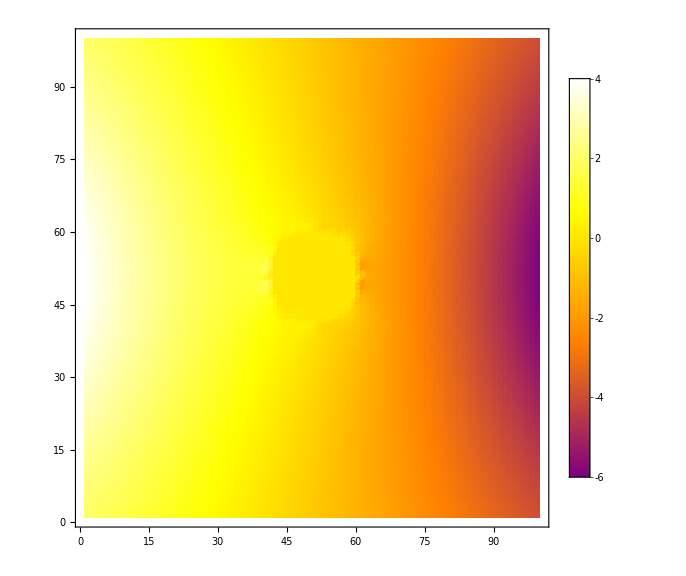

```mathematica
(*epilog2=ListContourPlot[compare1,ContourShading->None][[1]];*)
ListDensityPlot[comparep2,PlotTheme->"Detailed",ColorFunction->(Blend[{Purple,Orange,Yellow, White},#1]&), (*Epilog->epilog2,*) ImageSize->Large]
```

- Comparison GIF

```mathematica
Do[Export["/home/2317101h/year_3/group_project/compare/plates/pics/"<>ToString[i]<>".png",ListDensityPlot[ArrayReshape[Import["/home/2317101h/year_3/group_project/numerical_sol/section2.1/plates/anim/" <> ToString[i] <> ".dat"],{100,100}] - ArrayReshape[Import["/home/2317101h/year_3/group_project/analytical_sol/section2.1/plates/plates_anal.dat"],{100,100}],PlotTheme->"Detailed",ColorFunction->(Blend[{Purple,Orange,Yellow},#1]&), PlotLabel->"Iterations =" <>ToString[i] ]],{i, 0, 5000, 10}]
```